## Definiciones

```mathematica
Get["~/Documents/libs/QMB.wl"]
Get["/home/jadeleon/Documents/chaos_meets_channels/Mathematica_packages/Chaometer.wl"]
```

```mathematica
LogSpace[start_,end_,n_]:=Exp@Subdivide[Log[start],Log[end],n-1]
```

## Datos matrices de Choi

```mathematica
t0=0.1;tf=1000;
```

```mathematica
t=LogSpace[t0,tf,100];
```

```mathematica
L=7;
hx=1.;
```

```mathematica
points = Tuples[{#,#}]&[Subdivide[0., 3., 9]];
lenpoints = Length[points];
```

```mathematica
Do[
{hz,J} = points[[i]];

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop@Eigensystem[H];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"].Pinv;

chois=Table[ChoiMatrix[U[j],A,L],{j,t}];
Export["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[k],3,"0"]<>".csv",
Prepend[Flatten/@chois,{"Choi matrices from t=0 to t=1000 log spaced, 100 points. Initial state of environment generated with SeedRandom["<>ToString[x]<>"];ψ=RandomChainProductState[L-1];"}],
"CSV"];

,{i,lenpoints},{k,100}]
```

Evolucionando con el tiempo escalado como Jt:

```mathematica
AbsoluteTiming[
Do[
{hz,J} = points[[i]];

H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop@Eigensystem[H];

x=RandomInteger[100000];SeedRandom[x];
ψ=RandomChainProductState[L-1];
A=KroneckerProduct[IdentityMatrix[2^(L-1),SparseArray]/2,Dyad[ψ]];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];
ClearAll[U];U[t_]:=P.DiagonalMatrix[Exp[-I*eigenvals*t/J],TargetStructure->"Sparse"].Pinv;

chois=Table[ChoiMatrix[U[j],A,L],{j,t}];
Export["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[k],3,"0"]<>"_2.csv",
Prepend[Flatten/@chois,{"Choi matrices from t=0 to t=1000 log spaced, 100 points. Initial state of environment generated with SeedRandom["<>ToString[x]<>"];ψ=RandomChainProductState[L-1];"}],
"CSV"];

,{i,2,lenpoints},{k,100}]
]
```

{1094.38,Null}

```mathematica
26*44
```

19.0667

```mathematica
points=Complement[Tuples[Subdivide[0.,3.,9],2],Join[{#},{0.}]&/@Subdivide[0.,3.,9]][[46;;]]
lenpoints=Length[points]
```

{{1.66667,0.333333},{1.66667,0.666667},{1.66667,1.},{1.66667,1.33333},{1.66667,1.66667},{1.66667,2.},{1.66667,2.33333},{1.66667,2.66667},{1.66667,3.},{2.,0.333333},{2.,0.666667},{2.,1.},{2.,1.33333},{2.,1.66667},{2.,2.},{2.,2.33333},{2.,2.66667},{2.,3.},{2.33333,0.333333},{2.33333,0.666667},{2.33333,1.},{2.33333,1.33333},{2.33333,1.66667},{2.33333,2.},{2.33333,2.33333},{2.33333,2.66667},{2.33333,3.},{2.66667,0.333333},{2.66667,0.666667},{2.66667,1.},{2.66667,1.33333},{2.66667,1.66667},{2.66667,2.},{2.66667,2.33333},{2.66667,2.66667},{2.66667,3.},{3.,0.333333},{3.,0.666667},{3.,1.},{3.,1.33333},{3.,1.66667},{3.,2.},{3.,2.33333},{3.,2.66667},{3.,3.}}

45

```mathematica
Join[{#},{0}]&/@Subdivide[0.,3.,9]
```

{{0.,0},{0.333333,0},{0.666667,0},{1.,0},{1.33333,0},{1.66667,0},{2.,0},{2.33333,0},{2.66667,0},{3.,0}}

## Pureza de Choi promedio

```mathematica
points = Tuples[{#,#}]&[Subdivide[0., 3., 9]];
lenpoints = Length[points];
```

```mathematica
hz=3.;J=1.;
```

```mathematica
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"]],{i,100}];
```

```mathematica
chois//Dimensions
```

{100,100,4,4}

```mathematica
purities=Chop[Map[Purity[#]&,chois,{2}]];
```

```mathematica
AbsoluteTiming[
t01=0.1;tf=1000;
t02=170.735;
t=LogSpace[t01,tf,100];

points = Tuples[{#,#}]&[Subdivide[0., 3., 9]];
lenpoints = Length[points];

avgOftmpAvgsOfChoiPurity1={};
avgOftmpAvgsOfChoiPurity2={};

Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Graficar la pureza de Choi en el tiempo *)
(*fig=ListLogLinearPlot[Transpose[{t,#}]&/@purities,
PlotRange->{Full,{-0.02,1.02}},
Joined->True,
(*PlotMarkers->{Automatic,7},*)
PlotLabel->Style["Wisniacki, L=7, h_z="<>ToString[NumberForm[hz,{Infinity,2}]]<>", "<>"J="<>ToString[NumberForm[J,{Infinity,2}]]<>",\n100 estados aleatorios producto",Black,FontSize->22],
PlotStyle->Directive[Gray,Thickness[0.001]],
Frame->True,
FrameStyle->Directive[Black,FontSize->22],
FrameLabel->{TraditionalForm[HoldForm[t]],TraditionalForm[Tr[HoldForm[𝒟]^2]]},
Epilog->{Red,Thick,Opacity[0.75],InfiniteLine[{0.1,0.5},{1000,0.5}],Blue,Thick,Opacity[0.75],InfiniteLine[{0.1,0.25},{1000,0.25}]},
ImageSize->500
];*)

(*Export["~/Documents/chaos_meets_channels/ja_files/figs_ja/choi/purity_dynamics/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>".pdf",fig,"PDF"];*)

(* Calcular el promedio temporal de la pureza promedio de Choi de 0.1 a 1000 *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[t],{t,t01,tf}]/(tf-t01)
,{i,purities}];
AppendTo[avgOftmpAvgsOfChoiPurity1,{hz,J,Chop@Mean[tmpAvgChoiPurity],Chop@StandardDeviation[tmpAvgChoiPurity]}];

(* Calcular el promedio temporal de la pureza promedio de Choi de 170.735 a 1000 (últimos 20 tiempos en la escala log) *)
tmpAvgChoiPurity2=Table[
purityInterp=Interpolation[Transpose[{LogSpace[t02,tf,20],i[[-20;;]]}]]; 
NIntegrate[purityInterp[t],{t,t02,tf}]/(tf-t02)
,{i,purities}];
AppendTo[avgOftmpAvgsOfChoiPurity2,{hz,J,Chop@Mean[tmpAvgChoiPurity2],Chop@StandardDeviation[tmpAvgChoiPurity2]}];

,{j,lenpoints}]
]
```

{190.131,Null}

```mathematica
Select[avgOftmpAvgsOfChoiPurity2[[All,{1,2,3}]],#[[2]]!=0.&][[All,3]]//MinMax
```

{0.270583,0.542742}

```mathematica
Select[avgOftmpAvgsOfChoiPurity1[[All,{1,2,3}]],#[[2]]!=0.&][[All,3]]-Select[avgOftmpAvgsOfChoiPurity2[[All,{1,2,3}]],#[[2]]!=0.&][[All,3]]
```

{0.00659787,0.0034683,0.000483283,0.00219318,0.000543934,0.004376,-0.00652536,0.0100241,0.0252248,0.00387392,0.00120304,0.000611018,0.00058549,0.000879675,0.00370616,0.0139689,0.0187286,0.0116691,0.00280417,0.00129022,0.000897273,0.000744465,0.00051445,0.00141503,0.0061031,0.0113277,0.0106864,0.00664107,0.00317158,0.00167609,0.00164192,0.0019396,0.00311616,0.00342598,0.00684748,0.00842475,0.0104644,0.00514521,0.00339672,0.002934,0.00398884,0.00402478,0.00445084,0.00438902,0.00549068,0.0172486,0.0101155,0.00576021,0.00386517,0.00421747,0.00477184,0.00645954,0.0109897,0.00970227,0.0114177,0.0130468,0.00756961,0.00509665,0.00557852,0.00580831,0.00538458,0.00732613,0.0105004,0.00994077,0.00887823,0.0104509,0.00678036,0.00690809,0.00497047,0.00809232,0.00629438,0.00975733,0.010419,0.00788704,0.00575822,0.00939299,0.0078385,0.0108742,0.00499634,0.00798616,0.00766022,0.0114942,0.00953045,0.00577551,0.00694627,0.00828257,0.00811552,0.00974617,0.00453149,0.00989589}

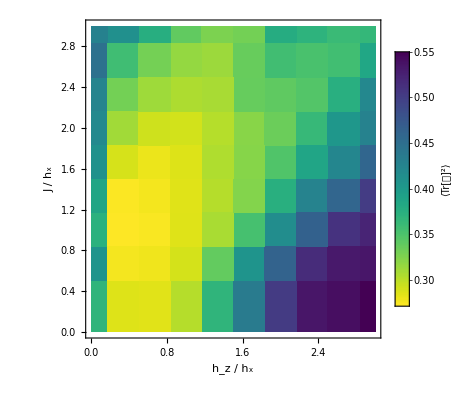

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[avgOftmpAvgsOfChoiPurity1[[All,{1,2,3}]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.27,0.56},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
avgOftmpAvgsOfChoiPurity1
```

{{0.,0.,1.,0},{0.,0.333333,0.369394,0.0154254},{0.,0.666667,0.407757,0.0117597},{0.,1.,0.373821,0.00987858},{0.,1.33333,0.387615,0.0115048},{0.,1.66667,0.411688,0.0234164},{0.,2.,0.421201,0.00817486},{0.,2.33333,0.42757,0.0085443},{0.,2.66667,0.449161,0.00872181},{0.,3.,0.43023,0.0104342},{0.333333,0.,1.,0},{0.333333,0.333333,0.284941,0.0133249},{0.333333,0.666667,0.275229,0.0106509},{0.333333,1.,0.271194,0.00693907},{0.333333,1.33333,0.272289,0.00544626},{0.333333,1.66667,0.288485,0.00845075},{0.333333,2.,0.310803,0.0104196},{0.333333,2.33333,0.330811,0.0147003},{0.333333,2.66667,0.358344,0.0154446},{0.333333,3.,0.412898,0.00996083},{0.666667,0.,1.,0},{0.666667,0.333333,0.28386,0.0119487},{0.666667,0.666667,0.277396,0.0106064},{0.666667,1.,0.273064,0.0074444},{0.666667,1.33333,0.275672,0.00767247},{0.666667,1.66667,0.279001,0.00741839},{0.666667,2.,0.291906,0.0104242},{0.666667,2.33333,0.311747,0.0116115},{0.666667,2.66667,0.330352,0.015316},{0.666667,3.,0.377421,0.01464},{1.,0.,1.,0},{1.,0.333333,0.302489,0.0157193},{1.,0.666667,0.289257,0.0149819},{1.,1.,0.284804,0.0144341},{1.,1.33333,0.284434,0.0131682},{1.,1.66667,0.285648,0.0128595},{1.,2.,0.290391,0.0121303},{1.,2.33333,0.30555,0.0157662},{1.,2.66667,0.316249,0.0175146},{1.,3.,0.339555,0.0173749},{1.33333,0.,1.,0},{1.33333,0.333333,0.36947,0.0329263},{1.33333,0.666667,0.338884,0.0347719},{1.33333,1.,0.307452,0.0275478},{1.33333,1.33333,0.302472,0.0208984},{1.33333,1.66667,0.304899,0.0235441},{1.33333,2.,0.30229,0.0178512},{1.33333,2.33333,0.307719,0.0210846},{1.33333,2.66667,0.312932,0.0198594},{1.33333,3.,0.326713,0.021487},{1.66667,0.,1.,0},{1.66667,0.333333,0.438101,0.0346632},{1.66667,0.666667,0.407616,0.0360239},{1.66667,1.,0.354294,0.0430722},{1.66667,1.33333,0.323786,0.0319083},{1.66667,1.66667,0.322211,0.0278457},{1.66667,2.,0.321396,0.0316305},{1.66667,2.33333,0.337313,0.0302131},{1.66667,2.66667,0.336658,0.0241751},{1.66667,3.,0.330949,0.0274614},{2.,0.,1.,0},{2.,0.333333,0.505906,0.0259674},{2.,0.666667,0.464874,0.0322768},{2.,1.,0.416598,0.0410813},{2.,1.33333,0.375369,0.0435952},{2.,1.66667,0.348395,0.0344399},{2.,2.,0.334921,0.0318334},{2.,2.33333,0.340888,0.0427783},{2.,2.66667,0.357503,0.0336004},{2.,3.,0.37912,0.0303864},{2.33333,0.,1.,0},{2.33333,0.333333,0.538443,0.0272668},{2.33333,0.666667,0.519811,0.0272778},{2.33333,1.,0.466941,0.0313189},{2.33333,1.33333,0.428496,0.0404386},{2.33333,1.66667,0.387794,0.0436227},{2.33333,2.,0.364418,0.0353704},{2.33333,2.33333,0.347199,0.0380485},{2.33333,2.66667,0.352447,0.0398076},{2.33333,3.,0.371364,0.0358725},{2.66667,0.,1.,0},{2.66667,0.333333,0.544406,0.0290819},{2.66667,0.666667,0.535857,0.0293925},{2.66667,1.,0.513849,0.019818},{2.66667,1.33333,0.46224,0.0398687},{2.66667,1.66667,0.424407,0.0433698},{2.66667,2.,0.404154,0.044477},{2.66667,2.33333,0.376055,0.0420696},{2.66667,2.66667,0.357288,0.0445271},{2.66667,3.,0.362152,0.0477369},{3.,0.,1.,0},{3.,0.333333,0.554236,0.0339667},{3.,0.666667,0.53812,0.0266871},{3.,1.,0.526481,0.0233364},{3.,1.33333,0.505159,0.0233459},{3.,1.66667,0.461772,0.0375009},{3.,2.,0.429066,0.04145},{3.,2.33333,0.422387,0.0446808},{3.,2.66667,0.386149,0.0474099},{3.,3.,0.366112,0.0494428}}

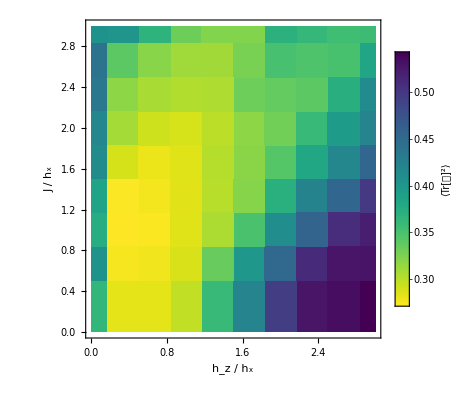

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[avgOftmpAvgsOfChoiPurity2[[All,{1,2,3}]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.27,0.56},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
r=avgOftmpAvgsOfChoiPurity1[[All,{1,2,3}]][[All,3]]-avgOftmpAvgsOfChoiPurity2[[All,{1,2,3}]][[All,3]]
```

{1.11022×10^-16,0.00659787,0.0034683,0.000483283,0.00219318,0.000543934,0.004376,-0.00652536,0.0100241,0.0252248,0.,0.00387392,0.00120304,0.000611018,0.00058549,0.000879675,0.00370616,0.0139689,0.0187286,0.0116691,9.10383×10^-15,0.00280417,0.00129022,0.000897273,0.000744465,0.00051445,0.00141503,0.0061031,0.0113277,0.0106864,2.9976×10^-15,0.00664107,0.00317158,0.00167609,0.00164192,0.0019396,0.00311616,0.00342598,0.00684748,0.00842475,0.,0.0104644,0.00514521,0.00339672,0.002934,0.00398884,0.00402478,0.00445084,0.00438902,0.00549068,1.55431×10^-15,0.0172486,0.0101155,0.00576021,0.00386517,0.00421747,0.00477184,0.00645954,0.0109897,0.00970227,6.21725×10^-15,0.0114177,0.0130468,0.00756961,0.00509665,0.00557852,0.00580831,0.00538458,0.00732613,0.0105004,-5.83977×10^-14,0.00994077,0.00887823,0.0104509,0.00678036,0.00690809,0.00497047,0.00809232,0.00629438,0.00975733,3.55271×10^-15,0.010419,0.00788704,0.00575822,0.00939299,0.0078385,0.0108742,0.00499634,0.00798616,0.00766022,-1.19904×10^-14,0.0114942,0.00953045,0.00577551,0.00694627,0.00828257,0.00811552,0.00974617,0.00453149,0.00989589}

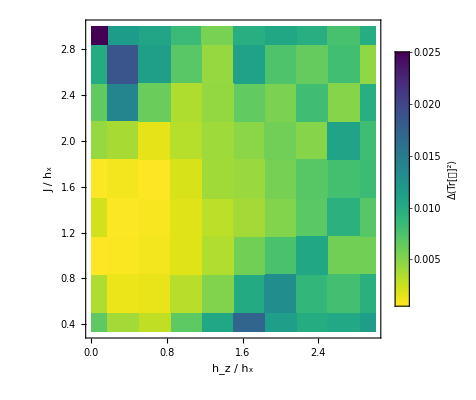

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[Table[Join[points[[i]],{Abs[r[[i]]]}],{i,lenpoints}],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Δ⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

### Fluctuaciones

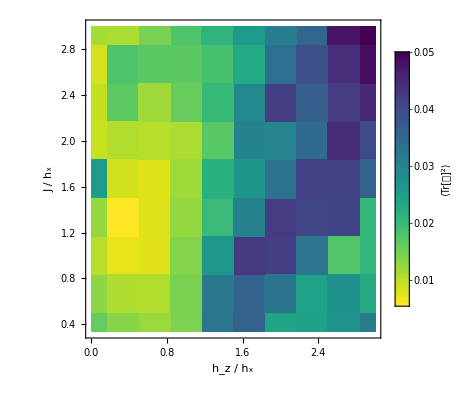

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[avgOftmpAvgsOfChoiPurity2[[All,{1,2,4}]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Log[10,Select[avgOftmpAvgsOfChoiPurity1[[All,{1,2,4}]],#[[2]]!=0.&][[All,3]]//MinMax]
```

{-2.2639,-1.3059}

```mathematica
10^-2.26
```

0.00549541

```mathematica
Select[avgOftmpAvgsOfChoiPurity1[[All,{1,2,4}]],#[[2]]!=0.&][[All,3]]//MinMax
```

{0.00544626,0.0494428}

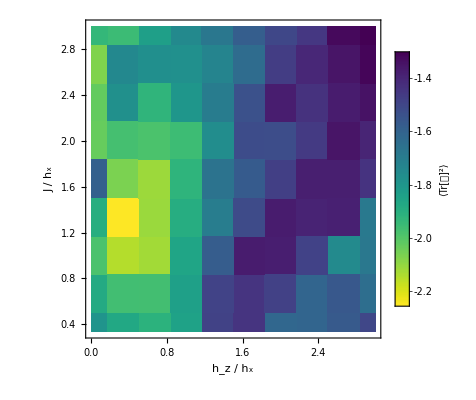

```mathematica
fontSize=18;

fig=ListDensityPlot[{#[[1]],#[[2]],Log10[#[[3]]]}&/@Select[avgOftmpAvgsOfChoiPurity2[[All,{1,2,4}]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

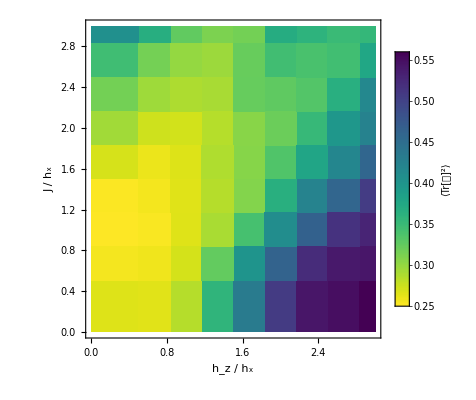

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[Chop[data[[All,1;;3]]],#[[2]]!=0.&&#[[1]]!=0&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,0.56},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[{Automatic,{0.25,0.56}},LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Export["/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/avgOver100InitStates_of_tmpAvgFrom0To1000LogSpaced100pts_of_choiPurity_wisniacki_L_7_hx_1.pdf",fig,"PDF"]
```

/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/avgOver100InitStates_of_tmpAvgFrom0To1000LogSpaced100pts_of_choiPurity_wisniacki_L_7_hx_1.pdf

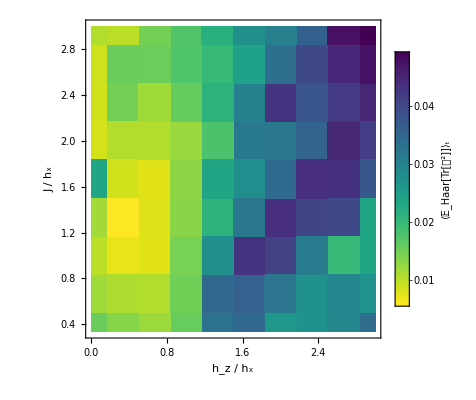

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[Chop[data[[All,{1,2,4}]]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
fontSize=18;

fig=ListDensityPlot[Chop[data[[All,{1,2,4}]]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
data2={};
Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>".csv"][[2;;]]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Calcular el promedio temporal de la pureza promedio de Choi *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[t],{t,170,tf}]/(tf-170)
,{i,purities}];

AppendTo[data2,{hz,J,Mean[tmpAvgChoiPurity],StandardDeviation[tmpAvgChoiPurity]}];

,{j,lenpoints}]
```

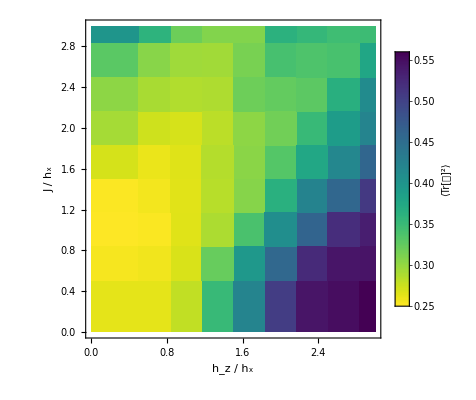

```mathematica
fontSize=18;

fig=ListDensityPlot[Select[Chop[data2[[All,1;;3]]],#[[2]]!=0.&&#[[1]]!=0&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->{0.25,0.56},
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[{Automatic,{0.25,0.56}},LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Export["/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/avgOver100InitStates_of_tmpAvgFrom170To1000LogSpaced20pts_of_choiPurity_wisniacki_L_7_hx_1.pdf",fig,"PDF"]
```

/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/avgOver100InitStates_of_tmpAvgFrom170To1000LogSpaced20pts_of_choiPurity_wisniacki_L_7_hx_1.pdf

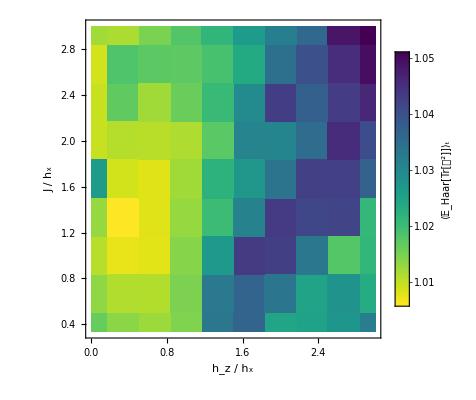

```mathematica
fontSize=18;

fig=ListDensityPlot[{#[[1]],#[[2]],Exp[#[[3]]]}&/@Select[Chop[data2[[All,{1,2,4}]]],#[[2]]!=0.&],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

```mathematica
Table[Join[points[[i]],{data2[[i,3]]-data[[i,3]]}],{i,lenpoints}]
```

{{0.,0.,0.0001},{0.,0.333333,-0.00686988},{0.,0.666667,-0.00342021},{0.,1.,-0.000634423},{0.,1.33333,-0.000984855},{0.,1.66667,-5.63526×10^-6},{0.,2.,-0.00455435},{0.,2.33333,0.00652318},{0.,2.66667,-0.00979451},{0.,3.,-0.0248322},{0.333333,0.,0.0001},{0.333333,0.333333,-0.00385242},{0.333333,0.666667,-0.00117843},{0.333333,1.,-0.000580968},{0.333333,1.33333,-0.000577231},{0.333333,1.66667,-0.000867547},{0.333333,2.,-0.00368273},{0.333333,2.33333,-0.0139127},{0.333333,2.66667,-0.0186121},{0.333333,3.,-0.0115593},{0.666667,0.,0.0001},{0.666667,0.333333,-0.00277347},{0.666667,0.666667,-0.00128038},{0.666667,1.,-0.000855365},{0.666667,1.33333,-0.000707262},{0.666667,1.66667,-0.000472201},{0.666667,2.,-0.00135071},{0.666667,2.33333,-0.0060869},{0.666667,2.66667,-0.0112392},{0.666667,3.,-0.010584},{1.,0.,0.0001},{1.,0.333333,-0.00660089},{1.,0.666667,-0.00314971},{1.,1.,-0.00162312},{1.,1.33333,-0.00162735},{1.,1.66667,-0.00191686},{1.,2.,-0.00306981},{1.,2.33333,-0.00339236},{1.,2.66667,-0.006789},{1.,3.,-0.00834162},{1.33333,0.,0.0001},{1.33333,0.333333,-0.0104304},{1.33333,0.666667,-0.00514587},{1.33333,1.,-0.00330239},{1.33333,1.33333,-0.00287678},{1.33333,1.66667,-0.00396839},{1.33333,2.,-0.0039927},{1.33333,2.33333,-0.00443252},{1.33333,2.66667,-0.00440526},{1.33333,3.,-0.00545281},{1.66667,0.,0.0001},{1.66667,0.333333,-0.0172093},{1.66667,0.666667,-0.0100419},{1.66667,1.,-0.00575958},{1.66667,1.33333,-0.00382005},{1.66667,1.66667,-0.00420572},{1.66667,2.,-0.00471912},{1.66667,2.33333,-0.00637943},{1.66667,2.66667,-0.0109302},{1.66667,3.,-0.0096238},{2.,0.,0.0001},{2.,0.333333,-0.0113248},{2.,0.666667,-0.0128949},{2.,1.,-0.00751505},{2.,1.33333,-0.00505906},{2.,1.66667,-0.00552477},{2.,2.,-0.00580639},{2.,2.33333,-0.00528075},{2.,2.66667,-0.00726492},{2.,3.,-0.0103633},{2.33333,0.,0.0001},{2.33333,0.333333,-0.00985796},{2.33333,0.666667,-0.0088629},{2.33333,1.,-0.0103874},{2.33333,1.33333,-0.00670263},{2.33333,1.66667,-0.00687152},{2.33333,2.,-0.00487984},{2.33333,2.33333,-0.00807797},{2.33333,2.66667,-0.00616371},{2.33333,3.,-0.00968081},{2.66667,0.,0.0001},{2.66667,0.333333,-0.0102853},{2.66667,0.666667,-0.00784464},{2.66667,1.,-0.00579335},{2.66667,1.33333,-0.00933159},{2.66667,1.66667,-0.00773309},{2.66667,2.,-0.0108828},{2.66667,2.33333,-0.00489075},{2.66667,2.66667,-0.00794844},{2.66667,3.,-0.00750209},{3.,0.,0.0001},{3.,0.333333,-0.011392},{3.,0.666667,-0.00939066},{3.,1.,-0.00564275},{3.,1.33333,-0.0068706},{3.,1.66667,-0.00823857},{3.,2.,-0.00804945},{3.,2.33333,-0.00964915},{3.,2.66667,-0.00454104},{3.,3.,-0.00983746}}

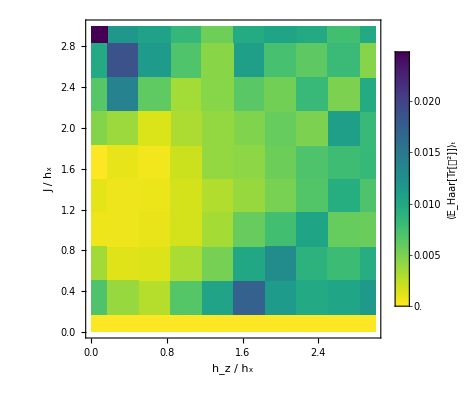

```mathematica
ListDensityPlot[Table[Join[points[[i]],{Abs[data2[[i,3]]-data[[i,3]]]}],{i,lenpoints}],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"⟨𝔼_Haar[Tr[𝒟^2]]⟩_t",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
AspectRatio->1
]
```

### Pureza promedio con el tiempo escalado como J t

Quiero obtener el mapa de pureza con los últimos 10,20 y 100 tiempos

```mathematica
tmpAvgHaarAvgChoiPurity={};
Do[
{hz,J} = points[[j]];

(* Importar las matrices de Choi *)
chois=Table[ArrayReshape[#,{4,4}]&/@ToExpression[Import["~/Documents/chaos_meets_channels/ja_files/data/chois/wisniacki/L_7_hx_1_hz_"<>ToString[NumberForm[hz,{Infinity,2}]]<>"_J_"<>ToString[NumberForm[J,{Infinity,2}]]<>"/"<>StringPadLeft[ToString[i],3,"0"]<>"_2.csv"]],{i,100}];

(* Calcular la pureza de las matrices de Choi *)
purities=Chop[Map[Purity[#]&,chois,{2}]];

(* Calcular el promedio temporal de la pureza promedio de Choi de 0.1 a 1000 *)
tmpAvgChoiPurity=Table[
purityInterp = Interpolation[Transpose[{t,i}]]; 
NIntegrate[purityInterp[i],{i,t[[-k]],t[[-1]]}]/(t[[-1]]-t[[-k]])
,{k,{100,20,10}},{i,purities}];
AppendTo[tmpAvgHaarAvgChoiPurity,Join[{hz,J},Mean/@tmpAvgChoiPurity]]

,{j,lenpoints}]
```

```mathematica
MinMax[tmpAvgHaarAvgChoiPurity[[All,#]]]&/@{3,4,5}
```

{{0.271194,0.541395},{0.270586,0.534876},{0.270615,0.533471}}

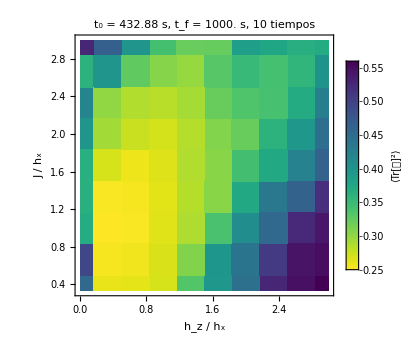

```mathematica
fig=ListDensityPlot[tmpAvgHaarAvgChoiPurity[[All,{1,2,5}]],
ColorFunction->(ResourceFunction["ViridisColor"][1-#]&),ColorFunctionScaling->True,
PlotRange->Full,
InterpolationOrder->0,
PlotLegends->Placed[BarLegend[{Automatic,{0.25,0.56}},LegendLabel->"⟨"<>ToString[TraditionalForm[HoldForm[Tr[HoldForm[𝒟]]^2]]]<>"⟩",LabelStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black]],Automatic],
Frame->True,
FrameStyle->Directive[FontFamily->"Arial",FontSize->fontSize,Black],
FrameLabel->{"h_z / h_x","J / h_x"},
PlotLabel->Style["t_0 = "<>ToString[NumberForm[t[[-10]],{Infinity,2}]]<>" s, "<>"t_f = "<>ToString[NumberForm[t[[-1]],{Infinity,0}]]<>" s"<>", 10 tiempos",Black,FontSize->20],
AspectRatio->1,
ImageSize->350
]
```

```mathematica
Export["/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_7_hx_1_9x10points_10timesLogSpaced.pdf",fig,"PDF"]
```

/home/jadeleon/Documents/chaos_meets_channels/ja_files/figs_ja/temporal_avg_haar_avg_choi_purity/wisniacki_open_L_7_hx_1_9x10points_10timesLogSpaced.pdf

## Graficando las gráficas

```mathematica
{means,stdDevs}=Transpose[{Mean[#],StandardDeviation[#]}&/@Transpose[purities]]
```

{{0.892121,0.873513,0.85251,0.82916,0.803702,0.77664,0.748833,0.72159,0.696728,0.676584,0.6639,0.661511,0.671765,0.695629,0.731527,0.774214,0.814221,0.838817,0.835426,0.797859,0.7337,0.667861,0.634399,0.652173,0.698294,0.717929,0.686144,0.642113,0.619457,0.602089,0.587484,0.581867,0.599422,0.597561,0.590012,0.725989,0.560638,0.718195,0.59984,0.586516,0.56502,0.508249,0.514584,0.534023,0.57688,0.590556,0.520944,0.47794,0.543843,0.622933,0.525225,0.538273,0.653157,0.499071,0.604811,0.528546,0.533467,0.446434,0.51385,0.439843,0.446957,0.481724,0.437796,0.426237,0.424153,0.429511,0.444134,0.410006,0.420281,0.394419,0.382072,0.384639,0.395917,0.387391,0.374266,0.376193,0.38549,0.37302,0.385006,0.361006,0.370805,0.366423,0.363971,0.375616,0.361343,0.356191,0.369675,0.369161,0.356982,0.366664,0.346273,0.345967,0.354887,0.355823,0.363786,0.339326,0.350022,0.364972,0.351512,0.353716},{0.0464217,0.0544517,0.0635041,0.0735426,0.0844392,0.0959357,0.107601,0.118789,0.128613,0.13595,0.13952,0.138059,0.13062,0.116986,0.09812,0.076463,0.0559557,0.042213,0.0427711,0.0602475,0.0878803,0.114393,0.127142,0.120009,0.101159,0.0918332,0.104512,0.120588,0.12247,0.120131,0.117962,0.111306,0.0985501,0.100392,0.102592,0.0583937,0.104738,0.0680159,0.0992491,0.0969976,0.0861347,0.107762,0.106046,0.0949025,0.100882,0.0989505,0.105964,0.120278,0.104915,0.0912403,0.103137,0.0896623,0.0678613,0.0962962,0.0586265,0.0767158,0.075955,0.0835584,0.0773941,0.0744775,0.0735822,0.0741707,0.074253,0.0692533,0.0716851,0.0620327,0.0673032,0.0598519,0.0675497,0.0593251,0.0598379,0.0577997,0.0584027,0.057477,0.0549049,0.0566224,0.0580535,0.0564445,0.0580576,0.0455425,0.0506459,0.0571211,0.0533521,0.0644748,0.0528166,0.0492082,0.066671,0.0572548,0.0548876,0.0507533,0.0510732,0.0532151,0.0539755,0.0505307,0.0577313,0.0465072,0.0489552,0.0577823,0.0586367,0.0478643}}

## fd

P.D(t).P†.σ.P.D^*(t).P^†

```mathematica
hx=1.;L=7;hz=0.5;J=1.;
```

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvals,eigenvecs}=Chop@Eigensystem[H];

P=Transpose[eigenvecs];Pinv=Conjugate[eigenvecs];

ClearAll[U];U[t_]:=DiagonalMatrix[Exp[-I*eigenvals*t],TargetStructure->"Sparse"]
```

```mathematica
paulisInEigenergyBasis=Chop[Pinv.Pauli[Join[{0},#]].P]&/@Tuples[Range[0,3],L-1];
MatrixForm/@paulisInEigenergyBasis;
```

```mathematica
U[0.1]
```

SparseArray[…]

```mathematica
pp1=Chop[P.Chop[U[0.1].#.Conjugate[U[0.1]]].Pinv]&/@paulisInEigenergyBasis;
```

```mathematica
t=0.1;MatrixForm[pp2=Chop[MatrixExp[-I*H*t].pauliStrings[[2]].MatrixExp[I*H*t]]]
```

(-0.00976079 | 0.994955+0.0978599 ⅈ | 0.000230065-0.00261968 ⅈ | -0.0196194+0.0013253 ⅈ | -1.09899×10^-10+2.35829×10^-9 ⅈ | 2.16877×10^-7-1.25926×10^-8 ⅈ | 8.52315×10^-8+0.0000105279 ⅈ | 0.000064338-0.0000117591 ⅈ
0.994955-0.0978599 ⅈ | 0.00976035 | 0.0194879+0.00262496 ⅈ | 0.0000336803+0.00263281 ⅈ | -2.17001×10^-7-1.38465×10^-8 ⅈ | 1.11872×10^-10-7.26444×10^-8 ⅈ | -0.0000653899-1.38015×10^-6 ⅈ | -1.65845×10^-6-0.0000103876 ⅈ
0.000230065+0.00261968 ⅈ | 0.0194879-0.00262496 ⅈ | 0.0294792 | 0.955683-0.292246 ⅈ | 3.53909×10^-7+0.0000105227 ⅈ | 0.0000652995-3.99641×10^-6 ⅈ | -3.16858×10^-10-2.29045×10^-9 ⅈ | -2.12947×10^-7+4.21791×10^-8 ⅈ
-0.0196194-0.0013253 ⅈ | 0.0000336803-0.00263281 ⅈ | 0.955683+0.292246 ⅈ | -0.0294788 | -0.0000647743-9.17783×10^-6 ⅈ | 1.22432×10^-6-0.0000104526 ⅈ | 2.16565×10^-7+1.88725×10^-8 ⅈ | 3.83388×10^-9+7.24592×10^-8 ⅈ
-1.09899×10^-10-2.35829×10^-9 ⅈ | -2.17001×10^-7+1.38465×10^-8 ⅈ | 3.53909×10^-7-0.0000105227 ⅈ | -0.0000647743+9.17783×10^-6 ⅈ | -0.00976079 | 0.994955+0.0978651 ⅈ | -0.000163845-0.00262501 ⅈ | -0.0192271+0.00390892 ⅈ
2.16877×10^-7+1.25926×10^-8 ⅈ | 1.11872×10^-10+7.26444×10^-8 ⅈ | 0.0000652995+3.99641×10^-6 ⅈ | 1.22432×10^-6+0.0000104526 ⅈ | 0.994955-0.0978651 ⅈ | 0.0097621 | 0.0196211+0.000015091 ⅈ | 0.00042444+0.00258569 ⅈ
8.52315×10^-8-0.0000105279 ⅈ | -0.0000653899+1.38015×10^-6 ⅈ | -3.16858×10^-10+2.29045×10^-9 ⅈ | 2.16565×10^-7-1.88725×10^-8 ⅈ | -0.000163845+0.00262501 ⅈ | 0.0196211-0.000015091 ⅈ | 0.0294792 | 0.955682-0.292252 ⅈ
0.000064338+0.0000117591 ⅈ | -1.65845×10^-6+0.0000103876 ⅈ | -2.12947×10^-7-4.21791×10^-8 ⅈ | 3.83388×10^-9-7.24592×10^-8 ⅈ | -0.0192271-0.00390892 ⅈ | 0.00042444-0.00258569 ⅈ | 0.955682+0.292252 ⅈ | -0.0294805)

```mathematica
Round[pp1[[2]],10.^-10]==Round[pp2,10.^-10]
```

True

```mathematica
MatrixPartialTrace[pp1[[1]],1,2]
```

{{2.,0,0,0},{0,2.,0,0},{0,0,2.,0},{0,0,0,2.}}

```mathematica
t=10.4;
RepeatedTiming[
(R=MatrixPartialTrace[Chop[P.Chop[U[t].paulisInEigenergyBasis[[2]].Conjugate[U[t]]]].Pinv,1,2]//Chop);
Chop[Tr[R.R]]
]
```

{0.000237006,2.65834}

```mathematica
t=10.4;
RepeatedTiming[
R=Chop[P.Chop[U[t].paulisInEigenergyBasis[[2]].Conjugate[U[t]]].Pinv];
]
```

{0.0000593152,Null}

```mathematica
t=10.4;
RepeatedTiming[
R1=Chop[P.U[t].paulisInEigenergyBasis[[2]].Conjugate[U[t]].Pinv];
]

RepeatedTiming[
Ucon=Conjugate[U[t]];uu=U[t];
R1=Chop[P.uu.paulisInEigenergyBasis[[2]].Ucon.Pinv];
]

RepeatedTiming[
R2=Chop[Transpose[Exp[-I*eigenvals*t]*Transpose[P]].paulisInEigenergyBasis[[2]].(Exp[I*eigenvals*t]*Pinv)];
]
```

{0.00584284,Null}

{0.00597795,Null}

{0.0164873,Null}

```mathematica
Round[R1,10.^-6]==Round[R2,10.^-6]
```

True

```mathematica
DiagonalMatrix[{1,2}].{{a,b},{c,d}}//MatrixForm
```

(a | b
2 c | 2 d)

```mathematica
DiagonalMatrix[{1,2,3}].{{a,b,c},{d,e,f},{g,h,i}}//MatrixForm
```

(a | b | c
2 d | 2 e | 2 f
3 g | 3 h | 3 i)

```mathematica
{{a,b,c},{d,e,f},{g,h,i}}.DiagonalMatrix[{1,2,3}]//MatrixForm
```

(a | 2 b | 3 c
d | 2 e | 3 f
g | 2 h | 3 i)

```mathematica
{1,2,3}*{{a,b,c},{d,e,f},{g,h,i}}//MatrixForm
```

(a | b | c
2 d | 2 e | 2 f
3 g | 3 h | 3 i)

```mathematica
ClearAll[t,UU,UUinv];UUinv[t_]:=Exp[I*eigenvals*t]*Pinv
UU[t_]:=Exp[-I*eigenvals*t]*P
```

```mathematica
t=0.1;
A=Chop[P.Chop[U[t].paulisInEigenergyBasis[[3]].Conjugate[U[t]]]];
tuples1=Tuples[Range[1,2^(L-1)],2];
tuples2=Tuples[Range[2^(L-1)+1,2^L],2];
RepeatedTiming[
r=Chop[(Sum[A[[#1,j]]*Pinv[[j,#2]],{j,2^L}]&@@@tuples1)+(Sum[A[[#1,j]]*Pinv[[j,#2]],{j,2^L}]&@@@tuples2)];
Chop[Conjugate[r].r]]
```

{0.0165707,64.}

```mathematica
Round[ArrayReshape[r,{8,8}],10.^-6]==Round[R,10.^-6]
```

True

```mathematica
A22//Dimensions
```

{16,16}

```mathematica
t=10.4;
A=Chop[P.Chop[U[t].paulisInEigenergyBasis[[2]].Conjugate[U[t]]]];
B=Pinv;
RepeatedTiming[
A11=A[[1;;2^(L-1),1;;2^(L-1)]];
A12=A[[1;;2^(L-1),2^(L-1)+1;;2^L]];
A21=A[[2^(L-1)+1;;2^L,1;;2^(L-1)]];
A22=A[[2^(L-1)+1;;2^L,2^(L-1)+1;;2^L]];
B11=B[[1;;2^(L-1),1;;2^(L-1)]];
B12=B[[1;;2^(L-1),2^(L-1)+1;;2^L]];
B21=B[[2^(L-1)+1;;2^L,1;;2^(L-1)]];
B22=B[[2^(L-1)+1;;2^L,2^(L-1)+1;;2^L]];
r=Chop[A11.B11+A12.B21+A21.B12+A22.B22];
Chop[Tr[r.r]]]
```

{0.223027,643.316}

```mathematica
t=10.4;
A=Chop[P.Chop[U[t].paulisInEigenergyBasis[[2]].Conjugate[U[t]]]];
B=Pinv;
RepeatedTiming[
{{A11,A12},{A21,A22}}=Partition[A,{2^(L-1),2^(L-1)}];
{{B11,B12},{B21,B22}}=Partition[B,{2^(L-1),2^(L-1)}];
r=Chop[A11.B11+A12.B21+A21.B12+A22.B22];
Chop[Tr[r.r]]]
```

{0.192657,643.316}

```mathematica
0.002*262000/60
```

8.73333

```mathematica
{{a11,a12},{a21,a22}}=Partition[A,{2^(L-1),2^(L-1)}];
```

```mathematica
ArrayReshape[Chop[(Sum[A[[#1,j]]*Pinv[[j,#2]],{j,8}]&@@@tuples1)+(Sum[A[[#1,j]]*Pinv[[j,#2]],{j,8}]&@@@tuples2)],{4,4}]//MatrixForm
```

(-0.608826 | -0.217944+0.00264003 ⅈ | 0.697529+0.0562077 ⅈ | 0.260528+0.168609 ⅈ
-0.217944-0.00264003 ⅈ | 0.0308382 | -0.64617-0.105746 ⅈ | -0.111122+0.137127 ⅈ
0.697529-0.0562077 ⅈ | -0.64617+0.105746 ⅈ | 0.336269 | -0.16159-0.0308812 ⅈ
0.260528-0.168609 ⅈ | -0.111122-0.137127 ⅈ | -0.16159+0.0308812 ⅈ | 0.241719)

```mathematica
RepeatedTiming[MatrixPartialTrace[Chop[P.Chop[U[0.1].pauliStrings[[2]].Conjugate[U[0.1]]]].Pinv,1,2];]
```

{0.000221122,Null}

```mathematica
RepeatedTiming[Chop[Table[Sum[A[[i,j]]*Pinv[[j,k]],{j,8}],{i,4},{k,4}]+Table[Sum[A[[i,j]]*Pinv[[j,k]],{j,8}],{i,5,8},{k,5,8}]]]
```

{0.000280168,{{-0.608826,-0.217944+0.00264003 ⅈ,0.697529+0.0562077 ⅈ,0.260528+0.168609 ⅈ},{-0.217944-0.00264003 ⅈ,0.0308382,-0.64617-0.105746 ⅈ,-0.111122+0.137127 ⅈ},{0.697529-0.0562077 ⅈ,-0.64617+0.105746 ⅈ,0.336269,-0.16159-0.0308812 ⅈ},{0.260528-0.168609 ⅈ,-0.111122-0.137127 ⅈ,-0.16159+0.0308812 ⅈ,0.241719}}}

```mathematica
RepeatedTiming[Chop[Table[Total[A[[i,#]]*Pinv[[#,k]]&/@{1,2,3,4,5,6,7,8}],{i,4},{k,4}]+Table[Total[A[[i,#]]*Pinv[[#,k]]#& /@{1,2,3,4,5,6,7,8}],{i,5,8},{k,5,8}]]]
```

{0.000429123,{{-1.55676-0.031893 ⅈ,-0.869784+0.296014 ⅈ,3.18311-0.533013 ⅈ,0.659021+0.279467 ⅈ},{-0.48971-0.373519 ⅈ,1.54275+0.0696412 ⅈ,-3.11284+0.271038 ⅈ,-1.57001+0.546407 ⅈ},{2.59612+0.53611 ⅈ,-2.64754-0.0952594 ⅈ,2.21976+0.00143973 ⅈ,-0.697434-0.077274 ⅈ},{0.515221-0.438138 ⅈ,-1.38509-0.608042 ⅈ,-0.990573-0.0567847 ⅈ,-0.524641-0.0555886 ⅈ}}}